### Data center solar modeling

This was originally written to study the ideal mix of solar and batteries for any kind of load in any kind of climate. This version has been localized on sun-abundant land (Texas) for AI training data centers (high capex, high uptime).
The general idea is to analyze revenue per unit capex (including the power system) as a function of solar array and battery size.

Casey Handmer 12/19/24

#### Download data

Download Texas data from https://www.nrel.gov/grid/solar-power-data.html

```mathematica
path="/home/chandmer/Documents/Solar\ Modeling/Texas/";
```

Having downloaded the Texas zip from the NREL website (a whole bunch of data from 2006!), let’s dump the file names and see what we have.

```mathematica
files=Import[path]
```

{Actual_32.05_-94.15_2006_UPV_95MW_5_Min.csv,Actual_32.05_-94.35_2006_UPV_27MW_5_Min.csv,Actual_32.35_-94.25_2006_UPV_122MW_5_Min.csv,Actual_32.45_-94.75_2006_DPV_35MW_5_Min.csv,Actual_32.45_-94.85_2006_DPV_35MW_5_Min.csv,Actual_32.55_-102.25_2006_UPV_118MW_5_Min.csv,Actual_32.55_-102.75_2006_UPV_118MW_5_Min.csv,Actual_32.55_-103.05_2006_UPV_118MW_5_Min.csv,Actual_32.55_-94.85_2006_DPV_35MW_5_Min.csv,Actual_32.65_-102.85_2006_UPV_118MW_5_Min.csv,Actual_32.65_-102.95_2006_UPV_118MW_5_Min.csv,Actual_32.65_-94.45_2006_UPV_54MW_5_Min.csv,Actual_32.75_-102.45_2006_UPV_17MW_5_Min.csv,Actual_32.85_-103.05_2006_UPV_84MW_5_Min.csv,Actual_32.95_-102.95_2006_UPV_17MW_5_Min.csv,Actual_32.95_-94.95_2006_UPV_27MW_5_Min.csv,Actual_33.05_-102.95_2006_UPV_67MW_5_Min.csv,Actual_33.05_-94.25_2006_UPV_54MW_5_Min.csv,Actual_33.15_-102.25_2006_UPV_50MW_5_Min.csv,Actual_33.15_-94.65_2006_UPV_14MW_5_Min.csv,Actual_33.25_-102.65_2006_UPV_17MW_5_Min.csv,Actual_33.35_-94.35_2006_UPV_95MW_5_Min.csv,Actual_33.45_-101.75_2006_UPV_84MW_5_Min.csv,Actual_33.45_-102.95_2006_UPV_151MW_5_Min.csv,Actual_33.45_-94.35_2006_DPV_27MW_5_Min.csv,Actual_33.45_-94.45_2006_DPV_27MW_5_Min.csv,Actual_33.55_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.55_-94.45_2006_DPV_27MW_5_Min.csv,Actual_33.55_-94.65_2006_UPV_136MW_5_Min.csv,Actual_33.65_-101.75_2006_DPV_37MW_5_Min.csv,Actual_33.65_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.65_-101.95_2006_DPV_37MW_5_Min.csv,Actual_33.65_-102.05_2006_UPV_34MW_5_Min.csv,Actual_33.65_-102.45_2006_UPV_168MW_5_Min.csv,Actual_33.75_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.75_-101.95_2006_UPV_101MW_5_Min.csv,Actual_33.75_-102.95_2006_UPV_50MW_5_Min.csv,Actual_34.05_-102.05_2006_UPV_151MW_5_Min.csv,Actual_34.15_-101.65_2006_UPV_151MW_5_Min.csv,Actual_34.35_-102.95_2006_UPV_50MW_5_Min.csv,Actual_34.55_-102.55_2006_UPV_168MW_5_Min.csv,Actual_34.65_-102.85_2006_UPV_34MW_5_Min.csv,Actual_34.95_-101.75_2006_DPV_27MW_5_Min.csv,Actual_34.95_-101.85_2006_DPV_27MW_5_Min.csv,Actual_34.95_-102.95_2006_UPV_67MW_5_Min.csv,Actual_35.05_-101.85_2006_DPV_27MW_5_Min.csv,Actual_35.15_-101.65_2006_UPV_101MW_5_Min.csv,Actual_35.35_-101.75_2006_DPV_28MW_5_Min.csv,Actual_35.35_-101.85_2006_DPV_28MW_5_Min.csv,Actual_35.35_-101.95_2006_UPV_17MW_5_Min.csv,Actual_35.35_-101.95_2006_UPV_67MW_5_Min.csv,Actual_35.45_-101.85_2006_DPV_28MW_5_Min.csv,Actual_35.75_-102.95_2006_UPV_151MW_5_Min.csv,Actual_35.85_-102.85_2006_UPV_17MW_5_Min.csv,Actual_36.05_-102.95_2006_UPV_17MW_5_Min.csv,Actual_36.25_-102.95_2006_UPV_84MW_5_Min.csv,DA_32.05_-94.15_2006_UPV_95MW_60_Min.csv,DA_32.05_-94.35_2006_UPV_27MW_60_Min.csv,DA_32.35_-94.25_2006_UPV_122MW_60_Min.csv,DA_32.45_-94.75_2006_DPV_35MW_60_Min.csv,DA_32.45_-94.85_2006_DPV_35MW_60_Min.csv,DA_32.55_-102.25_2006_UPV_118MW_60_Min.csv,DA_32.55_-102.75_2006_UPV_118MW_60_Min.csv,DA_32.55_-103.05_2006_UPV_118MW_60_Min.csv,DA_32.55_-94.85_2006_DPV_35MW_60_Min.csv,DA_32.65_-102.85_2006_UPV_118MW_60_Min.csv,DA_32.65_-102.95_2006_UPV_118MW_60_Min.csv,DA_32.65_-94.45_2006_UPV_54MW_60_Min.csv,DA_32.75_-102.45_2006_UPV_17MW_60_Min.csv,DA_32.85_-103.05_2006_UPV_84MW_60_Min.csv,DA_32.95_-102.95_2006_UPV_17MW_60_Min.csv,DA_32.95_-94.95_2006_UPV_27MW_60_Min.csv,DA_33.05_-102.95_2006_UPV_67MW_60_Min.csv,DA_33.05_-94.25_2006_UPV_54MW_60_Min.csv,DA_33.15_-102.25_2006_UPV_50MW_60_Min.csv,DA_33.15_-94.65_2006_UPV_14MW_60_Min.csv,DA_33.25_-102.65_2006_UPV_17MW_60_Min.csv,DA_33.35_-94.35_2006_UPV_95MW_60_Min.csv,DA_33.45_-101.75_2006_UPV_84MW_60_Min.csv,DA_33.45_-102.95_2006_UPV_151MW_60_Min.csv,DA_33.45_-94.35_2006_DPV_27MW_60_Min.csv,DA_33.45_-94.45_2006_DPV_27MW_60_Min.csv,DA_33.55_-101.85_2006_DPV_37MW_60_Min.csv,DA_33.55_-94.45_2006_DPV_27MW_60_Min.csv,DA_33.55_-94.65_2006_UPV_136MW_60_Min.csv,DA_33.65_-101.75_2006_DPV_37MW_60_Min.csv,DA_33.65_-101.85_2006_DPV_37MW_60_Min.csv,DA_33.65_-101.95_2006_DPV_37MW_60_Min.csv,DA_33.65_-102.05_2006_UPV_34MW_60_Min.csv,DA_33.65_-102.45_2006_UPV_168MW_60_Min.csv,DA_33.75_-101.85_2006_DPV_37MW_60_Min.csv,DA_33.75_-101.95_2006_UPV_101MW_60_Min.csv,DA_33.75_-102.95_2006_UPV_50MW_60_Min.csv,DA_34.05_-102.05_2006_UPV_151MW_60_Min.csv,DA_34.15_-101.65_2006_UPV_151MW_60_Min.csv,DA_34.35_-102.95_2006_UPV_50MW_60_Min.csv,DA_34.55_-102.55_2006_UPV_168MW_60_Min.csv,DA_34.65_-102.85_2006_UPV_34MW_60_Min.csv,DA_34.95_-101.75_2006_DPV_27MW_60_Min.csv,DA_34.95_-101.85_2006_DPV_27MW_60_Min.csv,DA_34.95_-102.95_2006_UPV_67MW_60_Min.csv,DA_35.05_-101.85_2006_DPV_27MW_60_Min.csv,DA_35.15_-101.65_2006_UPV_101MW_60_Min.csv,DA_35.35_-101.75_2006_DPV_28MW_60_Min.csv,DA_35.35_-101.85_2006_DPV_28MW_60_Min.csv,DA_35.35_-101.95_2006_UPV_17MW_60_Min.csv,DA_35.35_-101.95_2006_UPV_67MW_60_Min.csv,DA_35.45_-101.85_2006_DPV_28MW_60_Min.csv,DA_35.75_-102.95_2006_UPV_151MW_60_Min.csv,DA_35.85_-102.85_2006_UPV_17MW_60_Min.csv,DA_36.05_-102.95_2006_UPV_17MW_60_Min.csv,DA_36.25_-102.95_2006_UPV_84MW_60_Min.csv,HA4_32.05_-94.15_2006_UPV_95MW_60_Min.csv,HA4_32.05_-94.35_2006_UPV_27MW_60_Min.csv,HA4_32.35_-94.25_2006_UPV_122MW_60_Min.csv,HA4_32.45_-94.75_2006_DPV_35MW_60_Min.csv,HA4_32.45_-94.85_2006_DPV_35MW_60_Min.csv,HA4_32.55_-102.25_2006_UPV_118MW_60_Min.csv,HA4_32.55_-102.75_2006_UPV_118MW_60_Min.csv,HA4_32.55_-103.05_2006_UPV_118MW_60_Min.csv,HA4_32.55_-94.85_2006_DPV_35MW_60_Min.csv,HA4_32.65_-102.85_2006_UPV_118MW_60_Min.csv,HA4_32.65_-102.95_2006_UPV_118MW_60_Min.csv,HA4_32.65_-94.45_2006_UPV_54MW_60_Min.csv,HA4_32.75_-102.45_2006_UPV_17MW_60_Min.csv,HA4_32.85_-103.05_2006_UPV_84MW_60_Min.csv,HA4_32.95_-102.95_2006_UPV_17MW_60_Min.csv,HA4_32.95_-94.95_2006_UPV_27MW_60_Min.csv,HA4_33.05_-102.95_2006_UPV_67MW_60_Min.csv,HA4_33.05_-94.25_2006_UPV_54MW_60_Min.csv,HA4_33.15_-102.25_2006_UPV_50MW_60_Min.csv,HA4_33.15_-94.65_2006_UPV_14MW_60_Min.csv,HA4_33.25_-102.65_2006_UPV_17MW_60_Min.csv,HA4_33.35_-94.35_2006_UPV_95MW_60_Min.csv,HA4_33.45_-101.75_2006_UPV_84MW_60_Min.csv,HA4_33.45_-102.95_2006_UPV_151MW_60_Min.csv,HA4_33.45_-94.35_2006_DPV_27MW_60_Min.csv,HA4_33.45_-94.45_2006_DPV_27MW_60_Min.csv,HA4_33.55_-101.85_2006_DPV_37MW_60_Min.csv,HA4_33.55_-94.45_2006_DPV_27MW_60_Min.csv,HA4_33.55_-94.65_2006_UPV_136MW_60_Min.csv,HA4_33.65_-101.75_2006_DPV_37MW_60_Min.csv,HA4_33.65_-101.85_2006_DPV_37MW_60_Min.csv,HA4_33.65_-101.95_2006_DPV_37MW_60_Min.csv,HA4_33.65_-102.05_2006_UPV_34MW_60_Min.csv,HA4_33.65_-102.45_2006_UPV_168MW_60_Min.csv,HA4_33.75_-101.85_2006_DPV_37MW_60_Min.csv,HA4_33.75_-101.95_2006_UPV_101MW_60_Min.csv,HA4_33.75_-102.95_2006_UPV_50MW_60_Min.csv,HA4_34.05_-102.05_2006_UPV_151MW_60_Min.csv,HA4_34.15_-101.65_2006_UPV_151MW_60_Min.csv,HA4_34.35_-102.95_2006_UPV_50MW_60_Min.csv,HA4_34.55_-102.55_2006_UPV_168MW_60_Min.csv,HA4_34.65_-102.85_2006_UPV_34MW_60_Min.csv,HA4_34.95_-101.75_2006_DPV_27MW_60_Min.csv,HA4_34.95_-101.85_2006_DPV_27MW_60_Min.csv,HA4_34.95_-102.95_2006_UPV_67MW_60_Min.csv,HA4_35.05_-101.85_2006_DPV_27MW_60_Min.csv,HA4_35.15_-101.65_2006_UPV_101MW_60_Min.csv,HA4_35.35_-101.75_2006_DPV_28MW_60_Min.csv,HA4_35.35_-101.85_2006_DPV_28MW_60_Min.csv,HA4_35.35_-101.95_2006_UPV_17MW_60_Min.csv,HA4_35.35_-101.95_2006_UPV_67MW_60_Min.csv,HA4_35.45_-101.85_2006_DPV_28MW_60_Min.csv,HA4_35.75_-102.95_2006_UPV_151MW_60_Min.csv,HA4_35.85_-102.85_2006_UPV_17MW_60_Min.csv,HA4_36.05_-102.95_2006_UPV_17MW_60_Min.csv,HA4_36.25_-102.95_2006_UPV_84MW_60_Min.csv}

Select just the files which correspond to actual arrays.

```mathematica
files=Select[files,StringTake[#,6]=="Actual"&]
```

{Actual_32.05_-94.15_2006_UPV_95MW_5_Min.csv,Actual_32.05_-94.35_2006_UPV_27MW_5_Min.csv,Actual_32.35_-94.25_2006_UPV_122MW_5_Min.csv,Actual_32.45_-94.75_2006_DPV_35MW_5_Min.csv,Actual_32.45_-94.85_2006_DPV_35MW_5_Min.csv,Actual_32.55_-102.25_2006_UPV_118MW_5_Min.csv,Actual_32.55_-102.75_2006_UPV_118MW_5_Min.csv,Actual_32.55_-103.05_2006_UPV_118MW_5_Min.csv,Actual_32.55_-94.85_2006_DPV_35MW_5_Min.csv,Actual_32.65_-102.85_2006_UPV_118MW_5_Min.csv,Actual_32.65_-102.95_2006_UPV_118MW_5_Min.csv,Actual_32.65_-94.45_2006_UPV_54MW_5_Min.csv,Actual_32.75_-102.45_2006_UPV_17MW_5_Min.csv,Actual_32.85_-103.05_2006_UPV_84MW_5_Min.csv,Actual_32.95_-102.95_2006_UPV_17MW_5_Min.csv,Actual_32.95_-94.95_2006_UPV_27MW_5_Min.csv,Actual_33.05_-102.95_2006_UPV_67MW_5_Min.csv,Actual_33.05_-94.25_2006_UPV_54MW_5_Min.csv,Actual_33.15_-102.25_2006_UPV_50MW_5_Min.csv,Actual_33.15_-94.65_2006_UPV_14MW_5_Min.csv,Actual_33.25_-102.65_2006_UPV_17MW_5_Min.csv,Actual_33.35_-94.35_2006_UPV_95MW_5_Min.csv,Actual_33.45_-101.75_2006_UPV_84MW_5_Min.csv,Actual_33.45_-102.95_2006_UPV_151MW_5_Min.csv,Actual_33.45_-94.35_2006_DPV_27MW_5_Min.csv,Actual_33.45_-94.45_2006_DPV_27MW_5_Min.csv,Actual_33.55_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.55_-94.45_2006_DPV_27MW_5_Min.csv,Actual_33.55_-94.65_2006_UPV_136MW_5_Min.csv,Actual_33.65_-101.75_2006_DPV_37MW_5_Min.csv,Actual_33.65_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.65_-101.95_2006_DPV_37MW_5_Min.csv,Actual_33.65_-102.05_2006_UPV_34MW_5_Min.csv,Actual_33.65_-102.45_2006_UPV_168MW_5_Min.csv,Actual_33.75_-101.85_2006_DPV_37MW_5_Min.csv,Actual_33.75_-101.95_2006_UPV_101MW_5_Min.csv,Actual_33.75_-102.95_2006_UPV_50MW_5_Min.csv,Actual_34.05_-102.05_2006_UPV_151MW_5_Min.csv,Actual_34.15_-101.65_2006_UPV_151MW_5_Min.csv,Actual_34.35_-102.95_2006_UPV_50MW_5_Min.csv,Actual_34.55_-102.55_2006_UPV_168MW_5_Min.csv,Actual_34.65_-102.85_2006_UPV_34MW_5_Min.csv,Actual_34.95_-101.75_2006_DPV_27MW_5_Min.csv,Actual_34.95_-101.85_2006_DPV_27MW_5_Min.csv,Actual_34.95_-102.95_2006_UPV_67MW_5_Min.csv,Actual_35.05_-101.85_2006_DPV_27MW_5_Min.csv,Actual_35.15_-101.65_2006_UPV_101MW_5_Min.csv,Actual_35.35_-101.75_2006_DPV_28MW_5_Min.csv,Actual_35.35_-101.85_2006_DPV_28MW_5_Min.csv,Actual_35.35_-101.95_2006_UPV_17MW_5_Min.csv,Actual_35.35_-101.95_2006_UPV_67MW_5_Min.csv,Actual_35.45_-101.85_2006_DPV_28MW_5_Min.csv,Actual_35.75_-102.95_2006_UPV_151MW_5_Min.csv,Actual_35.85_-102.85_2006_UPV_17MW_5_Min.csv,Actual_36.05_-102.95_2006_UPV_17MW_5_Min.csv,Actual_36.25_-102.95_2006_UPV_84MW_5_Min.csv}

Make a quick map of where the arrays are in Texas.

```mathematica
arrLocs=Table[{ToExpression[StringTake[f,{8,12}]],ToExpression[StringDelete[StringTake[f,{14,20}],"_"]]},{f,files}]
```

{{32.05,-94.15},{32.05,-94.35},{32.35,-94.25},{32.45,-94.75},{32.45,-94.85},{32.55,-102.25},{32.55,-102.75},{32.55,-103.05},{32.55,-94.85},{32.65,-102.85},{32.65,-102.95},{32.65,-94.45},{32.75,-102.45},{32.85,-103.05},{32.95,-102.95},{32.95,-94.95},{33.05,-102.95},{33.05,-94.25},{33.15,-102.25},{33.15,-94.65},{33.25,-102.65},{33.35,-94.35},{33.45,-101.75},{33.45,-102.95},{33.45,-94.35},{33.45,-94.45},{33.55,-101.85},{33.55,-94.45},{33.55,-94.65},{33.65,-101.75},{33.65,-101.85},{33.65,-101.95},{33.65,-102.05},{33.65,-102.45},{33.75,-101.85},{33.75,-101.95},{33.75,-102.95},{34.05,-102.05},{34.15,-101.65},{34.35,-102.95},{34.55,-102.55},{34.65,-102.85},{34.95,-101.75},{34.95,-101.85},{34.95,-102.95},{35.05,-101.85},{35.15,-101.65},{35.35,-101.75},{35.35,-101.85},{35.35,-101.95},{35.35,-101.95},{35.45,-101.85},{35.75,-102.95},{35.85,-102.85},{36.05,-102.95},{36.25,-102.95}}

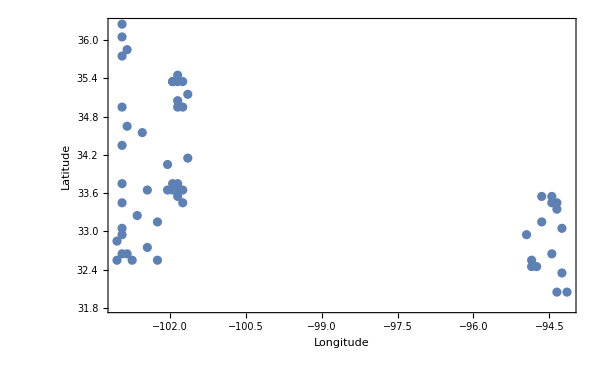

```mathematica
ListPlot[arrLocs[[All,{2,1}]],Frame->True,FrameLabel->{"Longitude","Latitude"},FrameStyle->Directive[14,Black],ImageSize->600]
```

Looks like the Mathematica geodata server is timing out :(

```mathematica
GeoListPlot[GeoPosition[arrLocs],GeoBackground->"Satellite",PlotMarkers->{Red,10}]
```

GeoGraphics::wdata: Unable to download data for ranges {{-103.513,-93.6914},{33.5962,39.2212}} and zoom level 6 from the Wolfram geo server.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: System`Private`SortOptions[{FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},«45»}] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[{FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},«45»}],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«44»}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[{FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},«45»}],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«44»}],{ImageSize,AspectRatio}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[GeoRange].

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (28): Connection timeout after 3000 ms"

GeoServer::styleres: Cannot download vector style resources.

-Graphics-

Unfortunately none near Van Horn, so we’ll take one from the North

```mathematica
raw=Import[path<>files[[-1]],"Data"];
```

One day’s worth of data points is 288 entries long.

```mathematica
day=12*24;
```

This is a whole year of data at 5 minute intervals!

Look at January 1

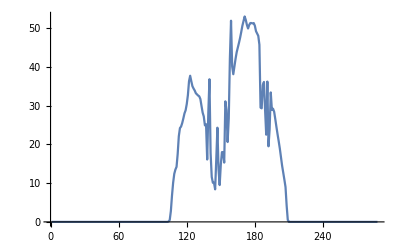

```mathematica
ListLinePlot[raw[[2;;day+1,2]],PlotRange->All]
```

Average daily power generation

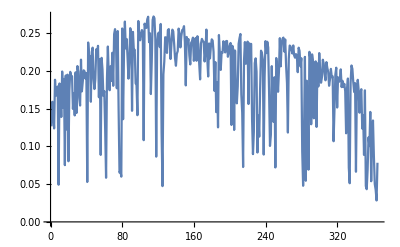

```mathematica
ListLinePlot[Total[Transpose[Partition[sol,day]]/day]]
```

Let’s clean it up a bit, standardize on a 1 MW equivalent array.

```mathematica
sol=raw[[2;;-1,2]]/84;
```

```mathematica
Clear[raw]
```

```mathematica
sol[[1;;200]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00119048,0.00595238,0.0333333,0.0809524,0.120238,0.147619,0.160714,0.169048,0.208333,0.263095,0.288095,0.292857,0.303571,0.317857,0.333333,0.342857,0.361905,0.389286,0.432143,0.44881,0.432143,0.416667,0.409524,0.403571,0.395238,0.391667,0.388095,0.385714,0.377381,0.355952,0.335714,0.32381,0.296429,0.3,0.191667,0.335714,0.438095,0.211905,0.138095,0.120238,0.120238,0.1,0.191667,0.289286,0.161905,0.113095,0.17619,0.214286,0.214286,0.182143,0.370238,0.342857,0.245238,0.317857,0.502381,0.617857,0.477381,0.453571,0.477381,0.50119,0.521429,0.535714,0.55,0.565476,0.583333,0.602381,0.616667,0.630952,0.620238,0.604762,0.594048,0.604762,0.610714,0.610714,0.609524,0.610714,0.602381,0.585714,0.578571,0.571429,0.544048,0.35119,0.34881,0.420238,0.429762,0.344048,0.267857,0.430952,0.232143,0.284524,0.397619,0.344048,0.347619,0.338095,0.315476,0.291667,0.269048}

Mean utilization

```mathematica
Total[sol]/Length[sol]
```

0.190943

Number of 5 minute intervals in a year.

```mathematica
Length[sol]
```

105120

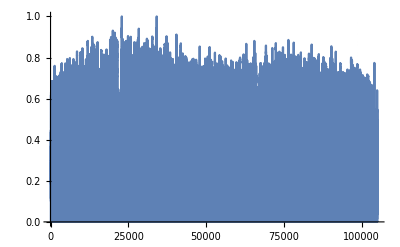

```mathematica
ListLinePlot[sol]
```

Every tenth day of the year.

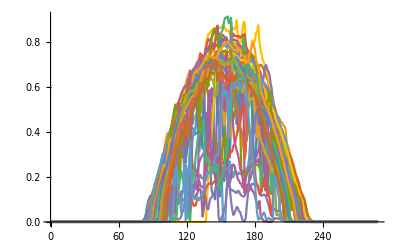

```mathematica
ListLinePlot[Partition[sol,day][[1;;-1;;10]]]
```

Power generated on any given day (MWh) for a 1 MW array.

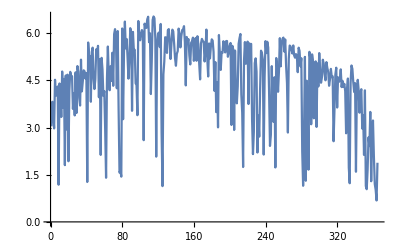

```mathematica
ListLinePlot[Total[Transpose[Partition[sol,day]]]/12]
```

Let’s baseline to a 1 MW array. Then set up a numerical array with loads of different sizes, and batteries of various sizes. If the battery is empty, the load is off. If the battery is full, no further charging can occur. Everything on 5 minute intervals. Assume battery starts full on Jan 1. 
Battery state is measured in MWh stored. So each 5 minute interval has to divide kWh or whatever by 12.

#### Time to run the sim

This function implements the above algorithm. It’s also nicely vectorized so you can choose a bunch of battery sizes (in MWh), and a bunch of load sizes (in MW) to feed of a standard 1 MW array whose 5 minute power generation is given by the sol vector. The function is a bit slow because it literally runs multiple if-then conditionals every 5 minutes for a whole year. For vectorization, these ifs are expressed using masks (sundisc etc) calculated using the Sign function. Otherwise we’d be here all day. There are probably more efficient ways to run this algorithm - it enables me to run approximately 6000 different systems in parallel on about 100,000 sequential data points in about 2 hours on a consumer-grade laptop. Importantly, it is straight-forward enough that I can debug it. 
It outputs a record of battery sizes, load sizes, a measure of battery state (roughly the fraction of the year it’s not fully discharged) and the total utilization of the load over the course of the year, which includes an assumption that it can throttle if only partial power is available.

```mathematica
Uptime[caps_,loads_,sol_]:=Catch[
batt=Table[cap,{Length[sol]},{cap,caps},{Length[loads]}];
util=0*batt;
ts=8760/Length[sol];(*hrs*)
loadsmat=Table[loads,{Length[caps]}];
capsmat=Transpose[Table[caps,{Length[loads]}]];

Do[
sundisc=0.5+0.5Sign[sol[[i]]-loadsmat];
battdisc=0.5+0.5Sign[batt[[i]]-ts(loadsmat-sol[[i]])];
capdisc=0.5+0.5Sign[batt[[i]]-capsmat];

util[[i]]=sundisc+(1-sundisc)battdisc+(1-sundisc)(1-battdisc)(sol[[i]]/loadsmat+batt[[i]]/(ts loadsmat));
batt[[i+1]]=sundisc (batt[[i]]+ts(sol[[i]]-loadsmat))+(1-sundisc)battdisc (batt[[i]]-ts(loadsmat-sol[[i]]))+(1-sundisc)(1-battdisc)*0.;
batt[[i+1]]=capdisc capsmat+(1-capdisc)batt[[i+1]];

,{i,1,Length[sol]-1}];Throw[Transpose[{capsmat,loadsmat,1-Total[1.-Sign[batt]]/Length[batt],ts Total[util]/8760.},{3,2,1}]]];
```

#### What do we do with this?

While the Uptime function allows us to generally analyze the battery/solar system dynamics for any given solar resource (sol), in this case we’re interested in a specific use case: hooking up a load with a given capex ($/MW) and maximizing productivity per dollar spent.

So we’re going to wrap the Uptime function in a new function that produces the all in system cost for a given battery and array size and assumptions about the baseline cost of each of these subsystems. This is the function we’re going to try to minimize.

```mathematica
AllInSystemCost[solarcost_,batterycost_,loadcost_,batterysize_,arraysize_,sol_]:=(#[[1]]*batterycost+solarcost +loadcost#[[2]])/(#[[2]]#[[4]])&[Uptime[{batterysize/arraysize},{1/arraysize},sol][[1,1]]]
```

```mathematica
AllInSystemCost[200000,200000,5000000,10,5,sol]
```

1.0523×10^7

To minimize this function, we calculate the cost under small variations to estimate the cost elasticity.

```mathematica
CostAndElasticity[solarcost_,batterycost_,loadcost_,batterysize_,arraysize_,sol_]:=Catch[
cost=AllInSystemCost[solarcost,batterycost,loadcost,batterysize,arraysize,sol];
costb=AllInSystemCost[solarcost,batterycost,loadcost,1.01batterysize+0.01,arraysize,sol];
costa=AllInSystemCost[solarcost,batterycost,loadcost,batterysize,1.01arraysize+0.01,sol];
Throw[{cost,costb,costa,(cost-costb)/cost,(cost-costa)/cost}]];
```

```mathematica
cae=CostAndElasticity[200000,200000,5000000,10,5,sol]
```

{1.0523×10^7,1.05017×10^7,1.0515×10^7,0.00202307,0.000761787}

Finally, we wrap the derivative function in a very crude gradient descent algorithm. It turns out that the underlying cost map is *just* regular enough that this approach is the best in terms of getting to a good enough answer with a minimum of brain sweat. I have a lot more experience with far more pathological cost functions in which we use the MCMC method, albeit at longer run time. For less pathological functions, Mathematica’s inbuilt “FindMinimum” function works quite nicely. It has a few hacks to ensure convergence across a wide range of initial conditions.

Output is {{solarcost $/MW, battery cost $/MWh, loadcost $/MW}, {arraysize (MW), battery size (MWh), load size (1 MW by definition)}, {array cost $, battery cost $, load cost $ (all normalized to 1 MW)}, {total power system cost $, all in system cost $, all in system cost normalized by utilization $}, {output from Uptime function, which is battery size relative to 1 MW array, load size relative to 1 MW array, battery utilization, and system utilization}}

```mathematica
FindMinimumSystemCost[solarcost_,batterycost_,loadcost_,sol_]:=Catch[
bi=Min[10.,10.loadcost/5000000];
ai=Min[10.,1.+9.loadcost/5000000];(*could make these better based on loadcost priors*)
amp=100+700. (loadcost/5000000)^1;
steps=10;
(*This is some hacky nonsense that improves convergence in special cases.*)
If[700000<loadcost<1300000,amp*=3];
If[80000000<loadcost,amp*=0.5];
costmin=10^10;
bimin=bi;
aimin=ai;
Do[
cae=CostAndElasticity[batterycost,solarcost,loadcost,bi,ai,sol];
If[cae[[1]]<costmin,aimin=ai;bimin=bi;costmin=cae[[1]];];
If[True,Print[{cae,bi,ai}]];
bi=Max[0.,bi+amp RandomReal[{0.1,1.}] cae[[4]]];
ai=Max[0.01,ai+amp RandomReal[{0.1,1.}]cae[[5]]];
,{steps}];
ut=Uptime[{bimin/aimin},{1/aimin},sol][[1,1]];
Throw[{{solarcost,batterycost ,loadcost},{aimin,bimin,1.},{solarcost aimin,batterycost bimin,loadcost},{solarcost aimin+batterycost bimin,solarcost aimin+batterycost bimin+loadcost,(solarcost aimin+batterycost bimin+loadcost)/ut[[-1]]},ut}]]
```

```mathematica
FindMinimumSystemCost[200000,200000,100000,sol]
```

{{1.66859×10^6,1.67923×10^6,1.65736×10^6,-0.0063749,0.00672967},0.2,1.18}

{{1.45358×10^6,1.45722×10^6,1.45688×10^6,-0.00250686,-0.00227189},0.,1.49534}

{{1.46445×10^6,1.47164×10^6,1.4594×10^6,-0.00490974,0.00344715},0.,1.27207}

{{1.45281×10^6,1.45659×10^6,1.45593×10^6,-0.00259921,-0.00214159},0.,1.48859}

{{1.44834×10^6,1.45323×10^6,1.44841×10^6,-0.0033772,-0.0000483746},0.,1.399}

{{1.44845×10^6,1.45333×10^6,1.44831×10^6,-0.00336945,0.0000936224},0.,1.39362}

{{1.44836×10^6,1.45323×10^6,1.44839×10^6,-0.00336213,-0.0000236344},0.,1.39803}

{{1.44838×10^6,1.45326×10^6,1.44837×10^6,-0.00336949,0.0000114355},0.,1.39688}

{{1.44838×10^6,1.45327×10^6,1.44837×10^6,-0.00337567,2.9087×10^-6},0.,1.39722}

{{1.44838×10^6,1.45327×10^6,1.44837×10^6,-0.00337574,1.83186×10^-6},0.,1.39726}

{{200000,200000,100000},{1.399,0.,1.},{279801.,0.,100000},{279801.,379801.,1.44834×10^6},{0.,0.714795,0.034161,0.262231}}

While not strictly necessary to understand data centers, whose cost is around $50,000,000/MW, we’ll find cost optimums across essentially the full range of potential load capexes, ranging from $10/kW (simple electric kettle) to $100,000/kW (state of the art supercomputer). What we will find is that for the lower capex loads, the optimal utilization is around 0.2, and optimal utilization grows with load capex up to about 0.98 for data centers. It’s surprising that it’s not higher, but it turns out that marginal costs exceed marginal gains at some point!

For this exercise, I’ve baselined solar cost at $200,000/MW, which is consistent with cutting edge costs for fixed panel systems such as Jurchen, combined with the cheapest available solar modules. Similarly, while we’ve seen BESS systems come in under $100,000/MWh, in this model battery costs include all the non generative, non load electrical infrastructure: switching, power lines, BMS, and so on. So call it $200,000/MWh also - for now.

```mathematica
AbsoluteTiming[frontierTable=Table[FindMinimumSystemCost[200000,200000,10000*10^i,sol],{i,0,4,0.1}];]
```

{6815.09,Null}

Export and save data

```mathematica
columnlabels={"solar cost $/MW","battery cost $/MWh","load cost $/MW","arraysize (MW)","battery size (MWh)","load size (1 MW by definition)","array cost $","battery cost $","load cost $ (all normalized to 1 MW)","total power system cost $","total system cost $","total system cost per utilization","battery size relative to 1 MW array","load size relative to 1 MW array","annual battery utilization","annual load utilization"};
```

```mathematica
Export["/home/chandmer/Documents/Solar Modeling/NorthTexas2.csv",Join[{columnlabels},Table[Flatten[f],{f,frontierTable}]]]
```

/home/chandmer/Documents/Solar Modeling/NorthTexas2.csv

```mathematica
Join[{columnlabels},Table[Flatten[f],{f,frontierTable}]]//MatrixForm
```

(solar cost $/MW | battery cost $/MWh | load cost $/MW | arraysize (MW) | battery size (MWh) | load size (1 MW by definition) | array cost $ | battery cost $ | load cost $ (all normalized to 1 MW) | total power system cost $ | total system cost $ | total system cost per utilization | battery size relative to 1 MW array | load size relative to 1 MW array | annual battery utilization | annual load utilization
200000 | 200000 | 1000 | 1.04325 | 0. | 1. | 208651. | 0. | 1000 | 208651. | 209651. | 1.05247×10^6 | 0. | 0.958538 | 0.0000475647 | 0.199199
200000 | 200000 | 10000. | 1.2133 | 0. | 1. | 242659. | 0. | 10000. | 242659. | 252659. | 1.09192×10^6 | 0. | 0.824202 | 0.00410008 | 0.231391
200000 | 200000 | 12589.3 | 1.22932 | 0. | 1. | 245864. | 0. | 12589.3 | 245864. | 258453. | 1.10294×10^6 | 0. | 0.813458 | 0.00525114 | 0.234331
200000 | 200000 | 15848.9 | 1.24367 | 0. | 1. | 248734. | 0. | 15848.9 | 248734. | 264583. | 1.11667×10^6 | 0. | 0.804073 | 0.00651636 | 0.23694
200000 | 200000 | 19952.6 | 1.2633 | 0. | 1. | 252659. | 0. | 19952.6 | 252659. | 272612. | 1.13371×10^6 | 0. | 0.791581 | 0.00884703 | 0.24046
200000 | 200000 | 25118.9 | 1.28552 | 0. | 1. | 257104. | 0. | 25118.9 | 257104. | 282223. | 1.15493×10^6 | 0. | 0.777896 | 0.011406 | 0.244363
200000 | 200000 | 31622.8 | 1.30012 | 0. | 1. | 260024. | 0. | 31622.8 | 260024. | 291647. | 1.18137×10^6 | 0. | 0.76916 | 0.0138128 | 0.246871
200000 | 200000 | 39810.7 | 1.31318 | 0. | 1. | 262636. | 0. | 39810.7 | 262636. | 302447. | 1.2143×10^6 | 0. | 0.761509 | 0.01621 | 0.249072
200000 | 200000 | 50118.7 | 1.32639 | 0. | 1. | 265278. | 0. | 50118.7 | 265278. | 315396. | 1.25533×10^6 | 0. | 0.753927 | 0.0189973 | 0.251245
200000 | 200000 | 63095.7 | 1.35076 | 0. | 1. | 270151. | 0. | 63095.7 | 270151. | 333247. | 1.30628×10^6 | 0. | 0.740326 | 0.0245244 | 0.255111
200000 | 200000 | 79432.8 | 1.37364 | 0. | 1. | 274729. | 0. | 79432.8 | 274729. | 354162. | 1.36968×10^6 | 0. | 0.727991 | 0.0292142 | 0.258573
200000 | 200000 | 100000. | 1.40301 | 0. | 1. | 280601. | 0. | 100000. | 280601. | 380601. | 1.44829×10^6 | 0. | 0.712755 | 0.0352264 | 0.262794
200000 | 200000 | 125893. | 1.42784 | 0. | 1. | 285569. | 0. | 125893. | 285569. | 411461. | 1.54581×10^6 | 0. | 0.700357 | 0.0400019 | 0.266178
200000 | 200000 | 158489. | 1.46674 | 0. | 1. | 293348. | 0. | 158489. | 293348. | 451838. | 1.66646×10^6 | 0. | 0.681783 | 0.0477549 | 0.271137
200000 | 200000 | 199526. | 1.51868 | 0. | 1. | 303737. | 0. | 199526. | 303737. | 503263. | 1.81573×10^6 | 0. | 0.658465 | 0.056992 | 0.277168
200000 | 200000 | 251189. | 1.57328 | 0. | 1. | 314657. | 0. | 251189. | 314657. | 565845. | 2.00034×10^6 | 0. | 0.635613 | 0.0652017 | 0.282875
200000 | 200000 | 316228. | 1.62434 | 0. | 1. | 324869. | 0. | 316228. | 324869. | 641097. | 2.22787×10^6 | 0. | 0.615633 | 0.0711948 | 0.287762
200000 | 200000 | 398107. | 1.72009 | 0. | 1. | 344018. | 0. | 398107. | 344018. | 742125. | 2.50757×10^6 | 0. | 0.581364 | 0.0814022 | 0.295954
200000 | 200000 | 501187. | 1.8844 | 0. | 1. | 376879. | 0. | 501187. | 376879. | 878067. | 2.85294×10^6 | 0. | 0.530674 | 0.0949772 | 0.307776
200000 | 200000 | 630957. | 1.93413 | 0.0133616 | 1. | 386827. | 2672.31 | 630957. | 389499. | 1.02046×10^6 | 3.26853×10^6 | 0.0069083 | 0.517027 | 0.206364 | 0.312207
200000 | 200000 | 794328. | 2.08694 | 0. | 1. | 417388. | 0. | 794328. | 417388. | 1.21172×10^6 | 3.792×10^6 | 0. | 0.479171 | 0.107667 | 0.319545
200000 | 200000 | 1.×10^6 | 2.35316 | 0.79068 | 1. | 470632. | 158136. | 1.×10^6 | 628768. | 1.62877×10^6 | 4.48503×10^6 | 0.336007 | 0.42496 | 0.306383 | 0.363157
200000 | 200000 | 1.25893×10^6 | 2.72251 | 1.47402 | 1. | 544503. | 294805. | 1.25893×10^6 | 839308. | 2.09823×10^6 | 5.21209×10^6 | 0.54142 | 0.367308 | 0.354243 | 0.402571
200000 | 200000 | 1.58489×10^6 | 3.26045 | 3.38262 | 1. | 652090. | 676523. | 1.58489×10^6 | 1.32861×10^6 | 2.91351×10^6 | 5.98072×10^6 | 1.03747 | 0.306706 | 0.445348 | 0.48715
200000 | 200000 | 1.99526×10^6 | 3.77113 | 4.57001 | 1. | 754226. | 914002. | 1.99526×10^6 | 1.66823×10^6 | 3.66349×10^6 | 6.74085×10^6 | 1.21184 | 0.265173 | 0.507021 | 0.543476
200000 | 200000 | 2.51189×10^6 | 4.33468 | 7.64673 | 1. | 866936. | 1.52935×10^6 | 2.51189×10^6 | 2.39628×10^6 | 4.90817×10^6 | 7.39835×10^6 | 1.76408 | 0.230697 | 0.632163 | 0.663414
200000 | 200000 | 3.16228×10^6 | 5.20683 | 10.812 | 1. | 1.04137×10^6 | 2.16241×10^6 | 3.16228×10^6 | 3.20377×10^6 | 6.36605×10^6 | 8.03002×10^6 | 2.07651 | 0.192055 | 0.767799 | 0.792782
200000 | 200000 | 3.98107×10^6 | 5.99079 | 13.2821 | 1. | 1.19816×10^6 | 2.65642×10^6 | 3.98107×10^6 | 3.85458×10^6 | 7.83565×10^6 | 8.788×10^6 | 2.21709 | 0.166923 | 0.875923 | 0.891631
200000 | 200000 | 5.01187×10^6 | 6.65241 | 13.6063 | 1. | 1.33048×10^6 | 2.72125×10^6 | 5.01187×10^6 | 4.05173×10^6 | 9.06361×10^6 | 9.92833×10^6 | 2.04531 | 0.150321 | 0.901218 | 0.912904
200000 | 200000 | 6.30957×10^6 | 6.95193 | 13.9357 | 1. | 1.39039×10^6 | 2.78714×10^6 | 6.30957×10^6 | 4.17753×10^6 | 1.04871×10^7 | 1.13415×10^7 | 2.00458 | 0.143845 | 0.915525 | 0.924669
200000 | 200000 | 7.94328×10^6 | 7.22787 | 14.2721 | 1. | 1.44557×10^6 | 2.85441×10^6 | 7.94328×10^6 | 4.29999×10^6 | 1.22433×10^7 | 1.30992×10^7 | 1.97459 | 0.138353 | 0.927045 | 0.934655
200000 | 200000 | 1.×10^7 | 7.51176 | 14.5358 | 1. | 1.50235×10^6 | 2.90717×10^6 | 1.×10^7 | 4.40952×10^6 | 1.44095×10^7 | 1.52878×10^7 | 1.93508 | 0.133125 | 0.936339 | 0.942548
200000 | 200000 | 1.25893×10^7 | 7.9291 | 14.7683 | 1. | 1.58582×10^6 | 2.95366×10^6 | 1.25893×10^7 | 4.53948×10^6 | 1.71287×10^7 | 1.80211×10^7 | 1.86255 | 0.126118 | 0.945424 | 0.95048
200000 | 200000 | 1.58489×10^7 | 8.20381 | 14.9008 | 1. | 1.64076×10^6 | 2.98017×10^6 | 1.58489×10^7 | 4.62093×10^6 | 2.04699×10^7 | 2.14384×10^7 | 1.81633 | 0.121895 | 0.950381 | 0.954823
200000 | 200000 | 1.99526×10^7 | 8.58735 | 15.1189 | 1. | 1.71747×10^6 | 3.02379×10^6 | 1.99526×10^7 | 4.74126×10^6 | 2.46939×10^7 | 2.57177×10^7 | 1.7606 | 0.11645 | 0.956982 | 0.96019
200000 | 200000 | 2.51189×10^7 | 9.36813 | 15.4255 | 1. | 1.87363×10^6 | 3.08511×10^6 | 2.51189×10^7 | 4.95874×10^6 | 3.00776×10^7 | 3.10835×10^7 | 1.6466 | 0.106745 | 0.965753 | 0.96764
200000 | 200000 | 3.16228×10^7 | 10.2429 | 15.4811 | 1. | 2.04858×10^6 | 3.09621×10^6 | 3.16228×10^7 | 5.14479×10^6 | 3.67676×10^7 | 3.77895×10^7 | 1.5114 | 0.0976288 | 0.97149 | 0.972958
200000 | 200000 | 3.98107×10^7 | 11.108 | 15.4348 | 1. | 2.22159×10^6 | 3.08697×10^6 | 3.98107×10^7 | 5.30856×10^6 | 4.51193×10^7 | 4.61796×10^7 | 1.38953 | 0.0900255 | 0.975704 | 0.977039
200000 | 200000 | 5.01187×10^7 | 9.73758 | 18.4671 | 1. | 1.94752×10^6 | 3.69343×10^6 | 5.01187×10^7 | 5.64094×10^6 | 5.57597×10^7 | 5.70034×10^7 | 1.89648 | 0.102695 | 0.977178 | 0.978181
200000 | 200000 | 6.30957×10^7 | 10.9891 | 17.9765 | 1. | 2.19781×10^6 | 3.5953×10^6 | 6.30957×10^7 | 5.79311×10^6 | 6.88888×10^7 | 7.01193×10^7 | 1.63585 | 0.0909995 | 0.981716 | 0.982452
200000 | 200000 | 7.94328×10^7 | 13.7464 | 15.982 | 1. | 2.74929×10^6 | 3.1964×10^6 | 7.94328×10^7 | 5.94569×10^6 | 8.53785×10^7 | 8.64362×10^7 | 1.16263 | 0.0727461 | 0.987081 | 0.987764
200000 | 200000 | 1.×10^8 | 13.2239 | 19.148 | 1. | 2.64479×10^6 | 3.8296×10^6 | 1.×10^8 | 6.47438×10^6 | 1.06474×10^8 | 1.07455×10^8 | 1.44798 | 0.0756205 | 0.990325 | 0.990878)

#### And now we do some plots, as a treat

This first plot shows how relative subsystems contribute to the overall cost, as a function of utilization. Utilization is not an independent variable, though, it’s just a property of a given system with a given load capex. So, in Texas, for loads with ideal utilization over 90%, almost all the total system cost is driven by load, not power system - which is great! Most of the money is spent on the parts that are doing useful work.

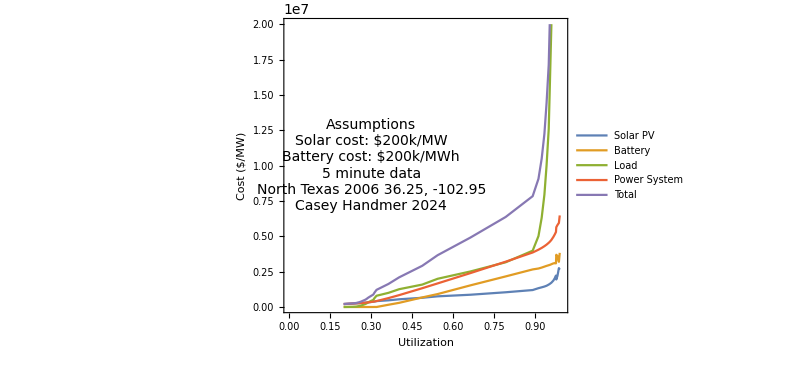

```mathematica
ListLinePlot[{Transpose[{frontierTable[[All,-1,-1]],frontierTable[[All,3,1]]}],Transpose[{frontierTable[[All,-1,-1]],frontierTable[[All,3,2]]}],Transpose[{frontierTable[[All,-1,-1]],frontierTable[[All,3,3]]}],Transpose[{frontierTable[[All,-1,-1]],frontierTable[[All,4,1]]}],Transpose[{frontierTable[[All,-1,-1]],frontierTable[[All,4,2]]}]},Frame->True,FrameStyle->Directive[14,Black],FrameLabel->{"Utilization","Cost ($/MW)"},ImageSize->600,PlotLegends->Placed[LineLegend[{"Solar PV","Battery","Load","Power System","Total"}],{0.7,0.7} ],PlotRange->{{0,1},{0*10^5,2*10^7}},ScalingFunctions->{"Linear","Linear"},Epilog->Text[Rotate[Style["Assumptions\nSolar cost: $200k/MW\nBattery cost: $200k/MWh\n5 minute data\nNorth Texas 2006 36.25, -102.95\nCasey Handmer 2024",14],0],{0.3,1.*10^7}]]
```

This chart shows how each of the various subcomponents’ costs vary as a function of load capex. Note, in particular, a swift phase change around the crucial step of $1,000,000/MW. Below this level, we have lower utilization systems with almost no batteries. Above it, we use batteries to drive utilization up, amortization down, and overall value up.

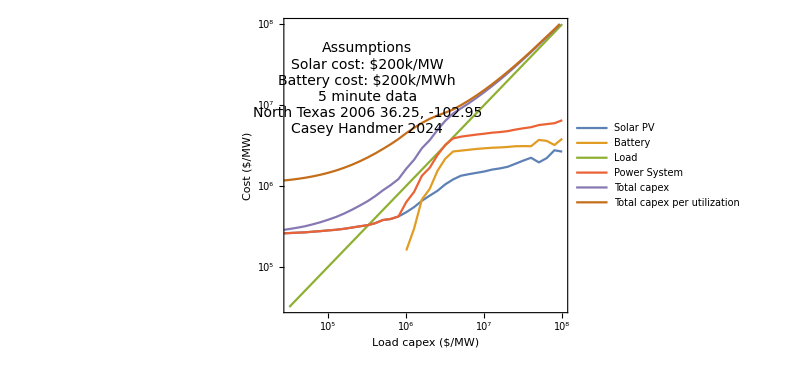

```mathematica
ListLinePlot[{Transpose[{frontierTable[[All,3,3]],frontierTable[[All,3,1]]}],Transpose[{frontierTable[[All,3,3]],frontierTable[[All,3,2]]}],Transpose[{frontierTable[[All,3,3]],frontierTable[[All,3,3]]}],Transpose[{frontierTable[[All,3,3]],frontierTable[[All,4,1]]}],Transpose[{frontierTable[[All,3,3]],frontierTable[[All,4,2]]}],Transpose[{frontierTable[[All,3,3]],frontierTable[[All,4,3]]}]},Frame->True,FrameStyle->Directive[14,Black],FrameLabel->{"Load capex ($/MW)","Cost ($/MW)"},ImageSize->600,PlotLegends->Placed[LineLegend[{"Solar PV","Battery","Load","Power System","Total capex","Total capex per utilization"}],{0.7,0.2} ],ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^4.5,10^8},{10^4.5,10^8}},Epilog->Text[Rotate[Style["Assumptions\nSolar cost: $200k/MW\nBattery cost: $200k/MWh\n5 minute data\nNorth Texas 2006 36.25, -102.95\nCasey Handmer 2024",14],0],{5.5,7.2}]]
```

This chart makes the relationship between utilization and load capex even more explicit. Note, however, even for $100,000,000/MW systems, even for a place as sunny as Texas, optimal utilization is not 100%.

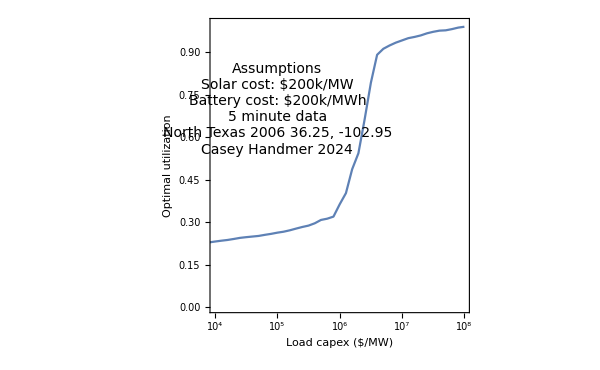

```mathematica
ListLinePlot[Transpose[{frontierTable[[All,3,3]],frontierTable[[All,5,4]]}],ScalingFunctions->{"Log10","Linear"},Frame->True,FrameStyle->Directive[14,Black],FrameLabel->{"Load capex ($/MW)","Optimal utilization"},ImageSize->600,PlotRange->{{10^4,10^8},{0,1}},Epilog->Text[Rotate[Style["Assumptions\nSolar cost: $200k/MW\nBattery cost: $200k/MWh\n5 minute data\nNorth Texas 2006 36.25, -102.95\nCasey Handmer 2024",14],0],{5,0.7}]]
```

This is a fun chart. It shows the cumulative cost of the power side system as a functional of utilization. The key takeaways is that, for systems that can live with 25% utilization, power is *cheap*. For systems that can use 90% utilization, power is still cheap (about $50/MWh) but not as cheap as pure solar. But even pushing to 99% utilization, solar and battery costs don’t go up all that much more. We’re still below $80/MWh, which is competitive with any other power source. What happens here, to drive this last little bit, is an expansion of the solar PV system to ensure adequate power generation for the overnight batteries, even on very gloomy days.  I also added a line corresponding the cost of not using available pure solar (no batteries) when available, for use cases with utilization even lower than raw power availability.

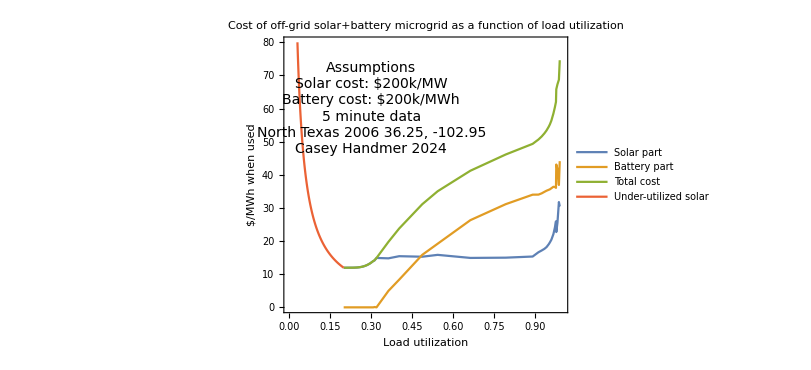

```mathematica
ListLinePlot[{Sort[Transpose[{frontierTable[[All,5,4]],(frontierTable[[All,4,1]]-frontierTable[[All,3,2]])/(10*8760*frontierTable[[All,5,4]])}][[1;;-1]]],Sort[Transpose[{frontierTable[[All,5,4]],frontierTable[[All,3,2]]/(10*8760*frontierTable[[All,5,4]])}][[1;;-1]]],Sort[Transpose[{frontierTable[[All,5,4]],frontierTable[[All,4,1]]/(10*8760*frontierTable[[All,5,4]])}][[1;;-1]]],Table[{u,frontierTable[[1,4,1]]/(10*8760*u)},{u,0.01,frontierTable[[1,5,4]],0.001}]},ScalingFunctions->{"Linear","Linear"},Frame->True,FrameStyle->Directive[14,Black],FrameLabel->{"Load utilization","$/MWh when used"},ImageSize->600,PlotRange->{{0,1},{0,80}},Epilog->Text[Rotate[Style["Assumptions\nSolar cost: $200k/MW\nBattery cost: $200k/MWh\n5 minute data\nNorth Texas 2006 36.25, -102.95\nCasey Handmer 2024",14],0],{0.3,60}],PlotLabel->Style["Cost of off-grid solar+battery microgrid as a function of load utilization",Black,16],PlotLegends->Placed[LineLegend[{"Solar part","Battery part","Total cost","Under-utilized solar"}],{0.7,0.8} ]]
```

Finally, we repeat the power generation graph from above, for direct comparison and replication of this study.

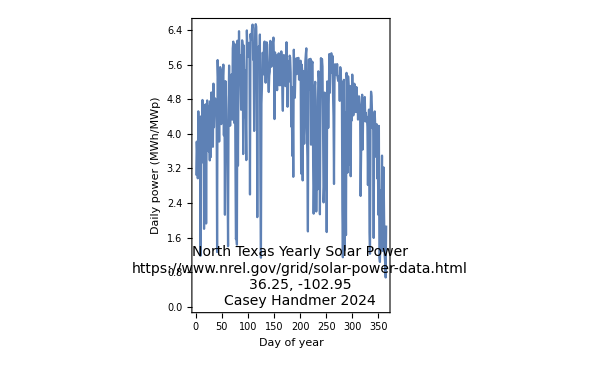

```mathematica
ListLinePlot[24Total[Transpose[Partition[sol,day]]/day],Frame->True,FrameStyle->Directive[14,Black],FrameLabel->{"Day of year","Daily power (MWh/MWp)"},ImageSize->600,PlotRange->All,Epilog->Text[Rotate[Style["North Texas Yearly Solar Power\nhttps://www.nrel.gov/grid/solar-power-data.html\n36.25, -102.95\nCasey Handmer 2024",14],0],{200,0.7}]]
```

#### Conclusions

Off grid pure solar+batteries are cost competitive for a range of loads and desired utilizations, particularly in sunny places with good solar resources. There is no need for gas back up, grid connection, or auxiliary generators. All these options are higher cost and lower reliability than a distributed solar array with battery storage. Nor is it necessary to read a crystal ball here. For any given load in any given place, keep adding solar and batteries until the overall productivity per dollar spent reaches a peak, and we’re done.